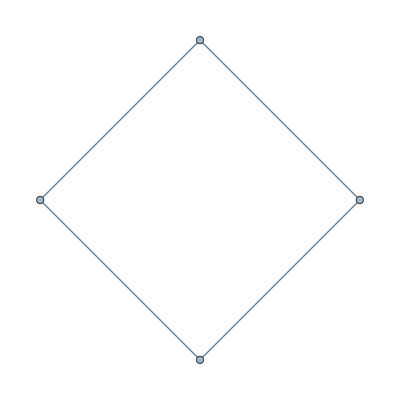
<|k→2,m→4,count→1,graphs→{-Graphics-},graph6→{>>graph6<<C]
}|>

```mathematica
(* ============================================================Compute F_k^{min} from your graph6 files (n=k+2)============================================================*)(* =====0) 清理环境=====*)ClearAll["Global`*"];

(* =====1) 基本设置=====*)
baseDir="C:\\Users\\Lenovo\\Desktop";
k=2;m=k+2;(* =====2) 导入 graph6 列表=====*)ClearAll[loadGraph6List];
loadGraph6List[dir_String,n_Integer]:=Module[{file,graphList},file=FileNameJoin[{dir,"graph"<>ToString[n]<>".g6"}];
graphList=Import[file,"Graph6"];
If[!ListQ[graphList],graphList={graphList}];
graphList];

graphList=loadGraph6List[baseDir,m];

(*（可选）如果你的 g6 文件不是“非同构图列表”，而是含重复标号图，可以用下面两行去重（会慢一些）：graphList=DeleteDuplicatesBy[graphList,CanonicalGraph];*)

(* =====3) 判定：是否属于 F_k^{min}=====*)
ClearAll[inFkMinQ];
inFkMinQ[g_Graph]:=Module[{verts,degList,degAssoc,edgesUV},verts=VertexList[g];
degList=VertexDegree[g];(*与 VertexList 顺序一致*)(*先过滤：最小度必须>=2*)If[Min[degList]<2,Return[False]];
(*把度数做成查表，避免反复计算*)degAssoc=AssociationThread[verts->degList];
(*边表转成 {u,v}*)edgesUV=EdgeList[g]/. UndirectedEdge[u_,v_]:>{u,v};
(*边极小：每条边至少有一个端点度=2*)AllTrue[edgesUV,(degAssoc[#[[1]]]==2||degAssoc[#[[2]]]==2)&]];

(*（可选）更“保险”的慢速验证版：逐边删除检查 ClearAll[inFkMinQslow];
inFkMinQslow[g_Graph]:=Module[{deg0,eds},deg0=Min[VertexDegree[g]];
If[deg0<2,Return[False]];
eds=EdgeList[g];
AllTrue[eds,(Min[VertexDegree[EdgeDelete[g,#]]]<=1)&]];*)

(* =====4) 计算并输出结果=====*)
FkMinGraphs=Select[graphList,inFkMinQ];

resFkMin=<|"k"->k,"m"->m,"count"->Length[FkMinGraphs],"graphs"->FkMinGraphs,"graph6"->(ExportString[#,"Graph6"]&/@FkMinGraphs)|>;

resFkMin
```

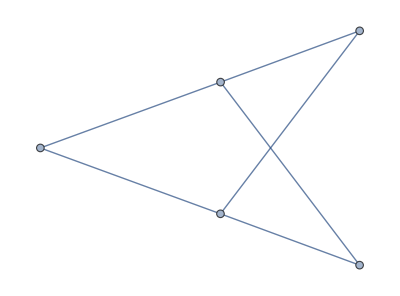
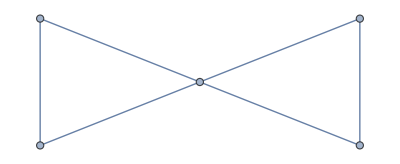
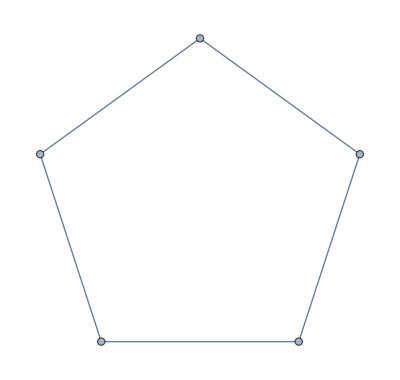
<|k→3,m→5,count→3,graphs→{-Graphics-,-Graphics-,-Graphics-},graph6→{>>graph6<<DFw
,>>graph6<<DQ{
,>>graph6<<DUW
}|>

```mathematica
(* ============================================================Compute F_k^{min} from your graph6 files (n=k+2)============================================================*)(* =====0) 清理环境=====*)ClearAll["Global`*"];

(* =====1) 基本设置=====*)
baseDir="C:\\Users\\Lenovo\\Desktop";
k=3;m=k+2;(* =====2) 导入 graph6 列表=====*)ClearAll[loadGraph6List];
loadGraph6List[dir_String,n_Integer]:=Module[{file,graphList},file=FileNameJoin[{dir,"graph"<>ToString[n]<>".g6"}];
graphList=Import[file,"Graph6"];
If[!ListQ[graphList],graphList={graphList}];
graphList];

graphList=loadGraph6List[baseDir,m];

(*（可选）如果你的 g6 文件不是“非同构图列表”，而是含重复标号图，可以用下面两行去重（会慢一些）：graphList=DeleteDuplicatesBy[graphList,CanonicalGraph];*)

(* =====3) 判定：是否属于 F_k^{min}=====*)
ClearAll[inFkMinQ];
inFkMinQ[g_Graph]:=Module[{verts,degList,degAssoc,edgesUV},verts=VertexList[g];
degList=VertexDegree[g];(*与 VertexList 顺序一致*)(*先过滤：最小度必须>=2*)If[Min[degList]<2,Return[False]];
(*把度数做成查表，避免反复计算*)degAssoc=AssociationThread[verts->degList];
(*边表转成 {u,v}*)edgesUV=EdgeList[g]/. UndirectedEdge[u_,v_]:>{u,v};
(*边极小：每条边至少有一个端点度=2*)AllTrue[edgesUV,(degAssoc[#[[1]]]==2||degAssoc[#[[2]]]==2)&]];

(*（可选）更“保险”的慢速验证版：逐边删除检查 ClearAll[inFkMinQslow];
inFkMinQslow[g_Graph]:=Module[{deg0,eds},deg0=Min[VertexDegree[g]];
If[deg0<2,Return[False]];
eds=EdgeList[g];
AllTrue[eds,(Min[VertexDegree[EdgeDelete[g,#]]]<=1)&]];*)

(* =====4) 计算并输出结果=====*)
FkMinGraphs=Select[graphList,inFkMinQ];

resFkMin=<|"k"->k,"m"->m,"count"->Length[FkMinGraphs],"graphs"->FkMinGraphs,"graph6"->(ExportString[#,"Graph6"]&/@FkMinGraphs)|>;

resFkMin
```

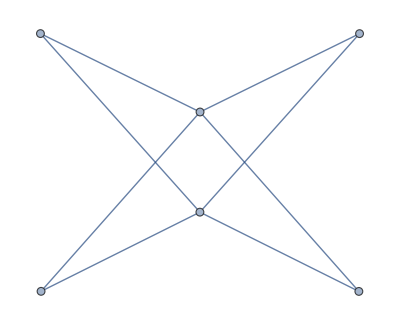
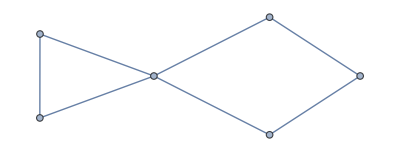
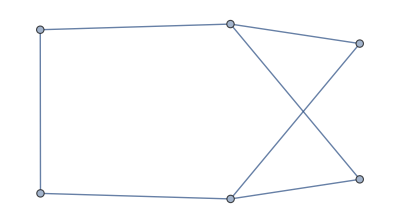
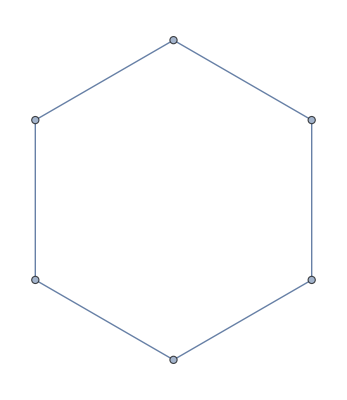
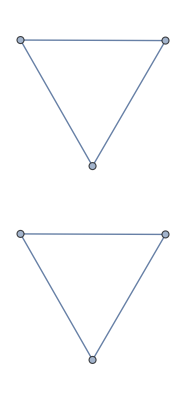
<|k→4,m→6,count→5,graphs→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},graph6→{>>graph6<<E?~o
,>>graph6<<ECZo
,>>graph6<<ECxo
,>>graph6<<EEh_
,>>graph6<<EQhO
}|>

```mathematica
(* ============================================================Compute F_k^{min} from your graph6 files (n=k+2)============================================================*)(* =====0) 清理环境=====*)ClearAll["Global`*"];

(* =====1) 基本设置=====*)
baseDir="C:\\Users\\Lenovo\\Desktop";
k=4;m=k+2;(* =====2) 导入 graph6 列表=====*)ClearAll[loadGraph6List];
loadGraph6List[dir_String,n_Integer]:=Module[{file,graphList},file=FileNameJoin[{dir,"graph"<>ToString[n]<>".g6"}];
graphList=Import[file,"Graph6"];
If[!ListQ[graphList],graphList={graphList}];
graphList];

graphList=loadGraph6List[baseDir,m];

(*（可选）如果你的 g6 文件不是“非同构图列表”，而是含重复标号图，可以用下面两行去重（会慢一些）：graphList=DeleteDuplicatesBy[graphList,CanonicalGraph];*)

(* =====3) 判定：是否属于 F_k^{min}=====*)
ClearAll[inFkMinQ];
inFkMinQ[g_Graph]:=Module[{verts,degList,degAssoc,edgesUV},verts=VertexList[g];
degList=VertexDegree[g];(*与 VertexList 顺序一致*)(*先过滤：最小度必须>=2*)If[Min[degList]<2,Return[False]];
(*把度数做成查表，避免反复计算*)degAssoc=AssociationThread[verts->degList];
(*边表转成 {u,v}*)edgesUV=EdgeList[g]/. UndirectedEdge[u_,v_]:>{u,v};
(*边极小：每条边至少有一个端点度=2*)AllTrue[edgesUV,(degAssoc[#[[1]]]==2||degAssoc[#[[2]]]==2)&]];

(*（可选）更“保险”的慢速验证版：逐边删除检查 ClearAll[inFkMinQslow];
inFkMinQslow[g_Graph]:=Module[{deg0,eds},deg0=Min[VertexDegree[g]];
If[deg0<2,Return[False]];
eds=EdgeList[g];
AllTrue[eds,(Min[VertexDegree[EdgeDelete[g,#]]]<=1)&]];*)

(* =====4) 计算并输出结果=====*)
FkMinGraphs=Select[graphList,inFkMinQ];

resFkMin=<|"k"->k,"m"->m,"count"->Length[FkMinGraphs],"graphs"->FkMinGraphs,"graph6"->(ExportString[#,"Graph6"]&/@FkMinGraphs)|>;

resFkMin
```

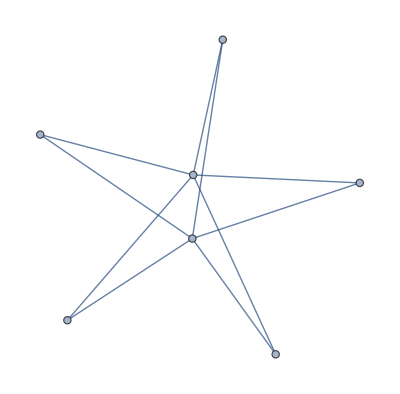
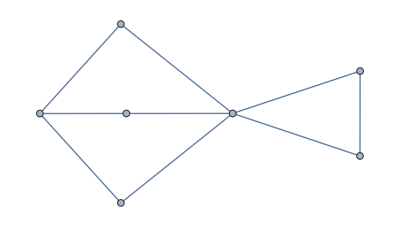
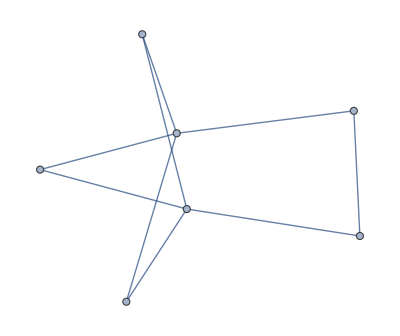
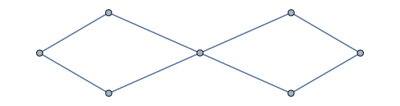
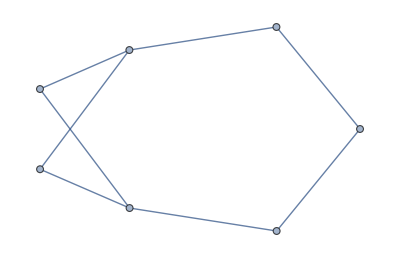
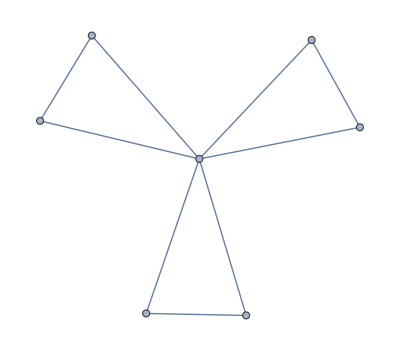
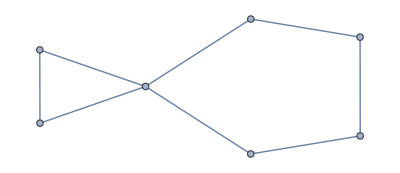
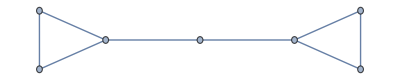
<|k→5,m→7,count→11,graphs→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},graph6→{>>graph6<<F?B~o
,>>graph6<<F?`vo
,>>graph6<<F?bro
,>>graph6<<F?ov_
,>>graph6<<F?qr_
,>>graph6<<FCOfw
,>>graph6<<FCQbo
,>>graph6<<FCQrO
,>>graph6<<FCR`o
,>>graph6<<FCdb?
,>>graph6<<FCp`_
}|>

```mathematica
(* ============================================================Compute F_k^{min} from your graph6 files (n=k+2)============================================================*)(* =====0) 清理环境=====*)ClearAll["Global`*"];

(* =====1) 基本设置=====*)
baseDir="C:\\Users\\Lenovo\\Desktop";
k=5;m=k+2;(* =====2) 导入 graph6 列表=====*)ClearAll[loadGraph6List];
loadGraph6List[dir_String,n_Integer]:=Module[{file,graphList},file=FileNameJoin[{dir,"graph"<>ToString[n]<>".g6"}];
graphList=Import[file,"Graph6"];
If[!ListQ[graphList],graphList={graphList}];
graphList];

graphList=loadGraph6List[baseDir,m];

(*（可选）如果你的 g6 文件不是“非同构图列表”，而是含重复标号图，可以用下面两行去重（会慢一些）：graphList=DeleteDuplicatesBy[graphList,CanonicalGraph];*)

(* =====3) 判定：是否属于 F_k^{min}=====*)
ClearAll[inFkMinQ];
inFkMinQ[g_Graph]:=Module[{verts,degList,degAssoc,edgesUV},verts=VertexList[g];
degList=VertexDegree[g];(*与 VertexList 顺序一致*)(*先过滤：最小度必须>=2*)If[Min[degList]<2,Return[False]];
(*把度数做成查表，避免反复计算*)degAssoc=AssociationThread[verts->degList];
(*边表转成 {u,v}*)edgesUV=EdgeList[g]/. UndirectedEdge[u_,v_]:>{u,v};
(*边极小：每条边至少有一个端点度=2*)AllTrue[edgesUV,(degAssoc[#[[1]]]==2||degAssoc[#[[2]]]==2)&]];

(*（可选）更“保险”的慢速验证版：逐边删除检查 ClearAll[inFkMinQslow];
inFkMinQslow[g_Graph]:=Module[{deg0,eds},deg0=Min[VertexDegree[g]];
If[deg0<2,Return[False]];
eds=EdgeList[g];
AllTrue[eds,(Min[VertexDegree[EdgeDelete[g,#]]]<=1)&]];*)

(* =====4) 计算并输出结果=====*)
FkMinGraphs=Select[graphList,inFkMinQ];

resFkMin=<|"k"->k,"m"->m,"count"->Length[FkMinGraphs],"graphs"->FkMinGraphs,"graph6"->(ExportString[#,"Graph6"]&/@FkMinGraphs)|>;

resFkMin
```

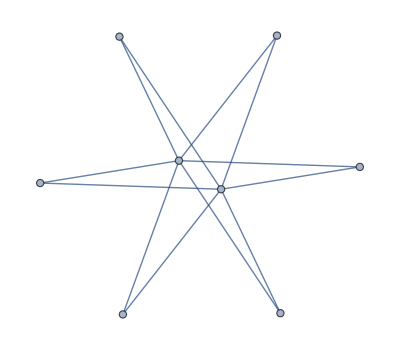
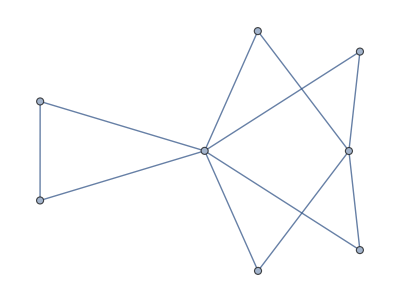
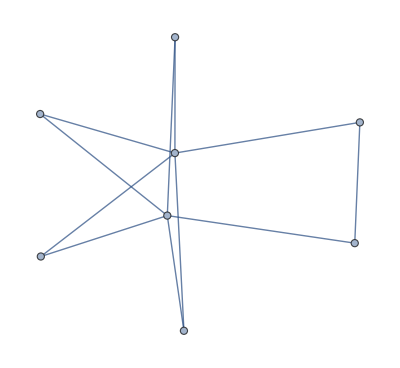
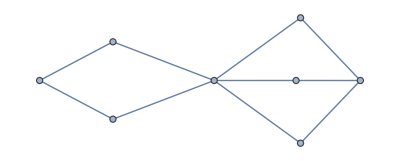
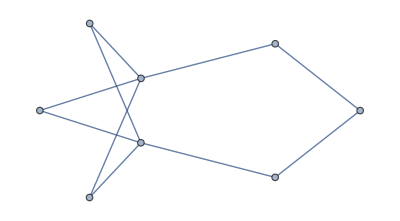
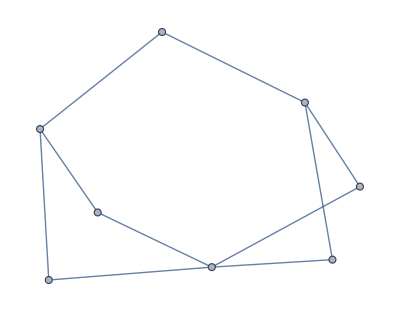
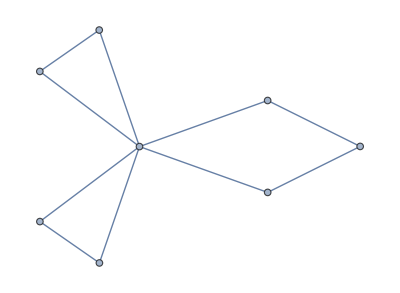
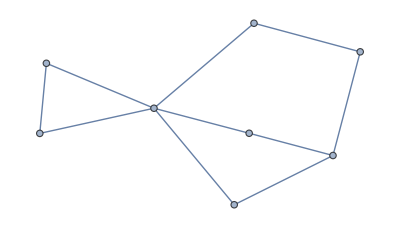
<|k→6,m→8,count→22,graphs→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},graph6→{>>graph6<<G??F~w
,>>graph6<<G?ABvw
,>>graph6<<G?AFrw
,>>graph6<<G?B@vo
,>>graph6<<G?BDro
,>>graph6<<G?Bcro
,>>graph6<<G?`@fw
,>>graph6<<G?`Dbw
,>>graph6<<G?`Drg
,>>graph6<<G?`F`w
,>>graph6<<G?`ado
,>>graph6<<G?`bco
,>>graph6<<G?`e`o
,>>graph6<<G?aJb_
,>>graph6<<G?b@bo
,>>graph6<<G?bB`o
,>>graph6<<G?qa`_
,>>graph6<<G?r@`_
,>>graph6<<GCOcbW
,>>graph6<<GCOe`W
,>>graph6<<GCOf?w
,>>graph6<<GCQR@O
}|>

```mathematica
(* ============================================================Compute F_k^{min} from your graph6 files (n=k+2)============================================================*)(* =====0) 清理环境=====*)ClearAll["Global`*"];

(* =====1) 基本设置=====*)
baseDir="C:\\Users\\Lenovo\\Desktop";
k=6;m=k+2;(* =====2) 导入 graph6 列表=====*)ClearAll[loadGraph6List];
loadGraph6List[dir_String,n_Integer]:=Module[{file,graphList},file=FileNameJoin[{dir,"graph"<>ToString[n]<>".g6"}];
graphList=Import[file,"Graph6"];
If[!ListQ[graphList],graphList={graphList}];
graphList];

graphList=loadGraph6List[baseDir,m];

(*（可选）如果你的 g6 文件不是“非同构图列表”，而是含重复标号图，可以用下面两行去重（会慢一些）：graphList=DeleteDuplicatesBy[graphList,CanonicalGraph];*)

(* =====3) 判定：是否属于 F_k^{min}=====*)
ClearAll[inFkMinQ];
inFkMinQ[g_Graph]:=Module[{verts,degList,degAssoc,edgesUV},verts=VertexList[g];
degList=VertexDegree[g];(*与 VertexList 顺序一致*)(*先过滤：最小度必须>=2*)If[Min[degList]<2,Return[False]];
(*把度数做成查表，避免反复计算*)degAssoc=AssociationThread[verts->degList];
(*边表转成 {u,v}*)edgesUV=EdgeList[g]/. UndirectedEdge[u_,v_]:>{u,v};
(*边极小：每条边至少有一个端点度=2*)AllTrue[edgesUV,(degAssoc[#[[1]]]==2||degAssoc[#[[2]]]==2)&]];

(*（可选）更“保险”的慢速验证版：逐边删除检查 ClearAll[inFkMinQslow];
inFkMinQslow[g_Graph]:=Module[{deg0,eds},deg0=Min[VertexDegree[g]];
If[deg0<2,Return[False]];
eds=EdgeList[g];
AllTrue[eds,(Min[VertexDegree[EdgeDelete[g,#]]]<=1)&]];*)

(* =====4) 计算并输出结果=====*)
FkMinGraphs=Select[graphList,inFkMinQ];

resFkMin=<|"k"->k,"m"->m,"count"->Length[FkMinGraphs],"graphs"->FkMinGraphs,"graph6"->(ExportString[#,"Graph6"]&/@FkMinGraphs)|>;

resFkMin
```

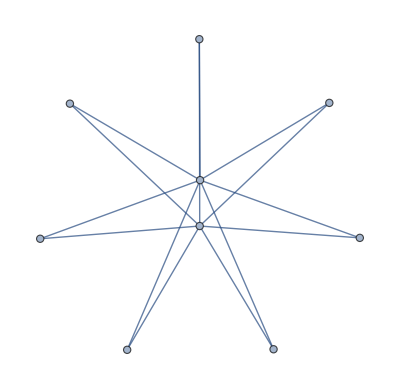
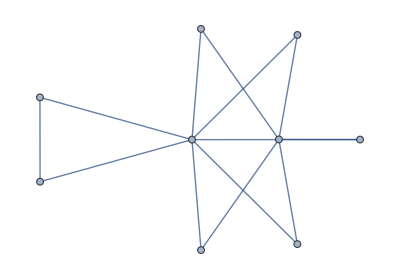
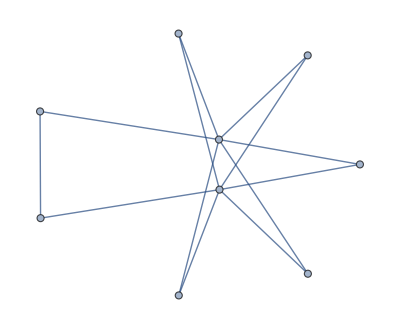
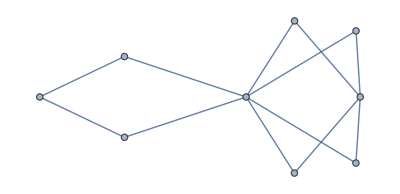
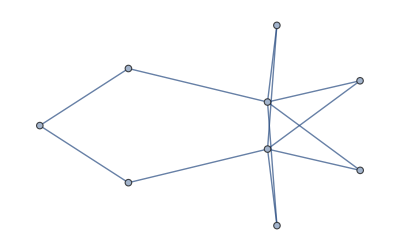
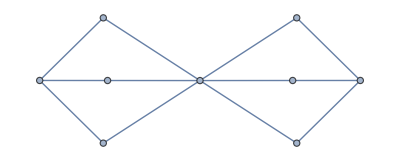
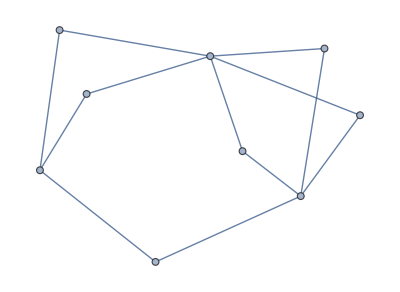
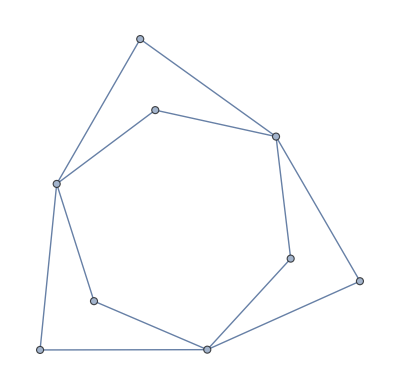
<|k→7,m→9,count→49,graphs→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},graph6→{>>graph6<<H???F~}
,>>graph6<<H??CBz}
,>>graph6<<H??CFx}
,>>graph6<<H??E@z{
,>>graph6<<H??EDx{
,>>graph6<<H??F?z{
,>>graph6<<H??FCx{
,>>graph6<<H??FeW{
,>>graph6<<H?AA@r}
,>>graph6<<H?AADp}
,>>graph6<<H?AADxy
,>>graph6<<H?AAFo}
,>>graph6<<H?AB?r{
,>>graph6<<H?ABAq{
,>>graph6<<H?ABBq[
,>>graph6<<H?ABCp{
,>>graph6<<H?ABEo{
,>>graph6<<H?ABbQ[
,>>graph6<<H?ABcXw
,>>graph6<<H?ABeO{
,>>graph6<<H?ACJpw
,>>graph6<<H?AE@p{
,>>graph6<<H?AEBo{
,>>graph6<<H?AF?xw
,>>graph6<<H?B@dPW
,>>graph6<<H?B@eOw
,>>graph6<<H?BD?pw
,>>graph6<<H?BDAow
,>>graph6<<H?BE@ow
,>>graph6<<H?`@?b~
,>>graph6<<H?`@C`}
,>>graph6<<H?`@Cpu
,>>graph6<<H?`@E_}
,>>graph6<<H?`@Eou
,>>graph6<<H?`@F_]
,>>graph6<<H?`@`bK
,>>graph6<<H?`@dPS
,>>graph6<<H?`@d`K
,>>graph6<<H?`@f?[
,>>graph6<<H?`CP`s
,>>graph6<<H?`CR_s
,>>graph6<<H?`D@`[
,>>graph6<<H?`D@pS
,>>graph6<<H?`DA_{
,>>graph6<<H?`DB_[
,>>graph6<<H?aJA_o
,>>graph6<<H?bAP_o
,>>graph6<<H?bB@_W
,>>graph6<<HCOcaOc
}|>

```mathematica
(* ============================================================Compute F_k^{min} from your graph6 files (n=k+2)============================================================*)(* =====0) 清理环境=====*)ClearAll["Global`*"];

(* =====1) 基本设置=====*)
baseDir="C:\\Users\\Lenovo\\Desktop";
k=7;m=k+2;(* =====2) 导入 graph6 列表=====*)ClearAll[loadGraph6List];
loadGraph6List[dir_String,n_Integer]:=Module[{file,graphList},file=FileNameJoin[{dir,"graph"<>ToString[n]<>".g6"}];
graphList=Import[file,"Graph6"];
If[!ListQ[graphList],graphList={graphList}];
graphList];

graphList=loadGraph6List[baseDir,m];

(*（可选）如果你的 g6 文件不是“非同构图列表”，而是含重复标号图，可以用下面两行去重（会慢一些）：graphList=DeleteDuplicatesBy[graphList,CanonicalGraph];*)

(* =====3) 判定：是否属于 F_k^{min}=====*)
ClearAll[inFkMinQ];
inFkMinQ[g_Graph]:=Module[{verts,degList,degAssoc,edgesUV},verts=VertexList[g];
degList=VertexDegree[g];(*与 VertexList 顺序一致*)(*先过滤：最小度必须>=2*)If[Min[degList]<2,Return[False]];
(*把度数做成查表，避免反复计算*)degAssoc=AssociationThread[verts->degList];
(*边表转成 {u,v}*)edgesUV=EdgeList[g]/. UndirectedEdge[u_,v_]:>{u,v};
(*边极小：每条边至少有一个端点度=2*)AllTrue[edgesUV,(degAssoc[#[[1]]]==2||degAssoc[#[[2]]]==2)&]];

(*（可选）更“保险”的慢速验证版：逐边删除检查 ClearAll[inFkMinQslow];
inFkMinQslow[g_Graph]:=Module[{deg0,eds},deg0=Min[VertexDegree[g]];
If[deg0<2,Return[False]];
eds=EdgeList[g];
AllTrue[eds,(Min[VertexDegree[EdgeDelete[g,#]]]<=1)&]];*)

(* =====4) 计算并输出结果=====*)
FkMinGraphs=Select[graphList,inFkMinQ];

resFkMin=<|"k"->k,"m"->m,"count"->Length[FkMinGraphs],"graphs"->FkMinGraphs,"graph6"->(ExportString[#,"Graph6"]&/@FkMinGraphs)|>;

resFkMin
```